```mathematica
P[x_,t_]=A[t]*Exp[-(a[t]*x[t]^2 + b[t]*x[t] + c[t])]
```

ⅇ^(-c[t]-b[t] x[t]-a[t] x[t]^2) A[t]

```mathematica
Log[P[x,t]] //PowerExpand
```

```mathematica
D[-c[t]+Log[A[t]]-b[t] x[t]-a[t] x[t]^2,t]
```

```mathematica
(-x[t]^2 a'[t]+A'[t]/A[t]-x[t] b'[t]-c'[t]-b[t] x'[t]-2 a[t] x[t] x'[t])^2
```

(-x[t]^2 a'[t]+A'[t]/A[t]-x[t] b'[t]-c'[t]-b[t] x'[t]-2 a[t] x[t] x'[t])^2

```mathematica
A[t_]:=(2 √π)/(√(k β (1+Coth[(k t1)/γ])))
```

```mathematica
a[t_]:= (ⅇ^(2 t (k/γ+1/τ)-(2 t)/τ) k^2 β)/(2 (k+(-1+ⅇ^((2 k t)/γ)) k))
```

```mathematica
b[t_]:= (ⅇ^(-(2 t)/τ) β (2 ⅇ^(t (k/γ+1/τ)+t/τ) F0 k γ (γ-k τ)-2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0 k^2 τ (γ-k τ)-2 ⅇ^(2 t (k/γ+1/τ)) F0 k (γ-k τ)^2))/(2 (k+(-1+ⅇ^((2 k t)/γ)) k) (γ-k τ)^2)
```

```mathematica
c[t_]:=1/(2 (k+(-1+ⅇ^((2 k t)/γ)) k) (γ-k τ)^2)ⅇ^(-(2 t)/τ) β (ⅇ^((2 t)/τ) F0^2 γ^2-2 ⅇ^((k t)/γ+t/τ) F0^2 k γ τ+ⅇ^((2 k t)/γ) F0^2 k^2 τ^2-2 ⅇ^(t (k/γ+1/τ)+t/τ) F0^2 γ (γ-k τ)+2 ⅇ^((k t)/γ+t (k/γ+1/τ)) F0^2 k τ (γ-k τ)+ⅇ^(2 t (k/γ+1/τ)) F0^2 (γ-k τ)^2)
```

```mathematica
Clear[A,a,b,c]
```

```mathematica
(-x[t]^2 a'[t]+A'[t]/A[t]-x[t] b'[t]-c'[t]-b[t] x'[t]-2 a[t] x[t] x'[t])^2 * P[x,t]
```

```mathematica
Integrate[ⅇ^(-c[t]-b[t] x[t]-a[t] x[t]^2) A[t] (-x[t]^2 a'[t]+A'[t]/A[t]-x[t] b'[t]-c'[t]-b[t] x'[t]-2 a[t] x[t] x'[t])^2,{x[t],-Infinity,Infinity}]
```

ConditionalExpression[1/(16 a[t]^(9/2) A[t])ⅇ^(b[t]^2/(4 a[t])-c[t]) √π (A[t]^2 b[t]^4 a'[t]^2-4 a[t] A[t]^2 b[t]^2 a'[t] (-3 a'[t]+b[t] b'[t])+4 a[t]^2 A[t] (-2 b[t]^2 a'[t] A'[t]+A[t] (3 a'[t]^2+b[t]^2 b'[t]^2+2 b[t] a'[t] (-3 b'[t]+b[t] c'[t])))+32 a[t]^5 A[t]^2 x'[t]^2+16 a[t]^4 ((A'[t]-A[t] c'[t])^2+2 A[t]^2 b'[t] x'[t])-8 a[t]^3 A[t] (-b'[t] (A[t] b'[t]+2 b[t] (A'[t]-A[t] c'[t]))+2 a'[t] (A'[t]-A[t] c'[t]+2 A[t] b[t] x'[t]))), ]

```mathematica
1/(16 a[t]^(9/2) A[t])ⅇ^(b[t]^2/(4 a[t])-c[t]) √π (A[t]^2 b[t]^4 a'[t]^2-4 a[t] A[t]^2 b[t]^2 a'[t] (-3 a'[t]+b[t] b'[t])+4 a[t]^2 A[t] (-2 b[t]^2 a'[t] A'[t]+A[t] (3 a'[t]^2+b[t]^2 b'[t]^2+2 b[t] a'[t] (-3 b'[t]+b[t] c'[t])))+32 a[t]^5 A[t]^2 x'[t]^2+16 a[t]^4 ((A'[t]-A[t] c'[t])^2+2 A[t]^2 b'[t] x'[t])-8 a[t]^3 A[t] (-b'[t] (A[t] b'[t]+2 b[t] (A'[t]-A[t] c'[t]))+2 a'[t] (A'[t]-A[t] c'[t]+2 A[t] b[t] x'[t])))//FullSimplify
```

(2 √2 ⅇ^(-2 t (k/γ+1/τ)) π √(k β) ((-ⅇ^((k t)/γ)+ⅇ^(t/τ)) F0-ⅇ^(t (k/γ+1/τ)) (γ-k τ) x'[t])^2)/((γ-k τ)^2 √(k β (1+Coth[(k t1)/γ])))

```mathematica
(-x[t]^2 a'[t]+A'[t]/A[t]-x[t] b'[t]-c'[t]-b[t] x'[t]-2 a[t] x[t] x'[t])^2//FullSimplify
```

(ⅇ^(-4 t (k/γ+1/τ)) β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (γ-k τ) (F0-k x[t]))^2 ((ⅇ^((k t)/γ)-ⅇ^(t/τ)) F0+ⅇ^(t (k/γ+1/τ)) (γ-k τ) x'[t])^2)/(γ-k τ)^4

```mathematica
(2 √2 ⅇ^(-2 t (k/γ+1/τ)) π √(k β) ((-ⅇ^((k t)/γ)+ⅇ^(t/τ)) F0-ⅇ^(t (k/γ+1/τ)) (γ-k τ) x'[t])^2)/((γ-k τ)^2 √(k β (1+Coth[(k t1)/γ])))/((ⅇ^(-4 t (k/γ+1/τ)) β^2 (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (γ-k τ) (F0-k x[t]))^2 ((ⅇ^((k t)/γ)-ⅇ^(t/τ)) F0+ⅇ^(t (k/γ+1/τ)) (γ-k τ) x'[t])^2)/(γ-k τ)^4)//FullSimplify
```

(2 √2 ⅇ^(2 t (k/γ+1/τ)) π √(k β) (γ-k τ)^2)/(β^2 √(k β (1+Coth[(k t1)/γ])) (-ⅇ^(t/τ) F0 γ+ⅇ^((k t)/γ) F0 k τ+ⅇ^(t (k/γ+1/τ)) (γ-k τ) (F0-k x[t]))^2)

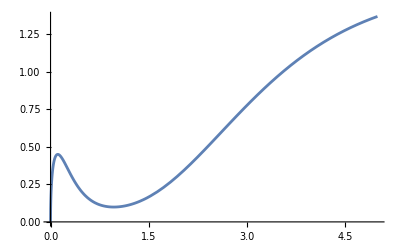

```mathematica
Plot[(2 √2 ⅇ^(-2 t (k/γ+1/τ)) π √(k β) ((-ⅇ^((k t)/γ)+ⅇ^(t/τ)) F0-ⅇ^(t (k/γ+1/τ)) (γ-k τ) x'[t])^2)/((γ-k τ)^2 √(k β (1+Coth[(k t1)/γ])))/.{x'[t]->0.5,F0->1,k->1, τ->1, γ->0.99,β->1,t1->t},{t,0,5}]
```

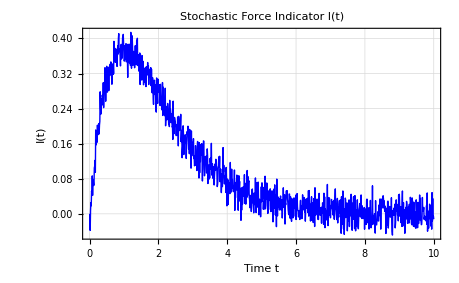

```mathematica
(*Parameters-adjust these to match your simulation*)gamma=0.999;
k=1.0;
tau=1.0;
F0=1.0;
T=1.0;
beta=1/T;

(*Import the data file*)
data=Import["average_derivative.dat","Table"];
times=data[[All,1]];
xDerivatives=data[[All,2]];

(*Define the function*)
IofT[t_,xPrime_]:=xPrime;


(*Create pairs of {time,I(t)}*)
results=Table[{times[[i]],IofT[times[[i]],xDerivatives[[i]]]},{i,Length[times]}];

(*Plot the results*)
ListPlot[results,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"Time t","I(t)"},PlotLabel->"Stochastic Force Indicator I(t)",GridLines->Automatic,PlotStyle->{Thick,Blue}]

(*Optional:Export the results to a new file*)
Export["I_of_t_results.dat",results,"Table"];
```

NonlinearModelFit::nrlnum: The function value {1.+1. #^1.-1. Time,1.01,1.05784,1.02239,1.01469,1.03171,1.00806,1.02617,0.993447,1.04796,1.02151,1.03476,1.05544,1.06406,1.03499,1.04151,«19»,1.08839,1.11214,1.09937,1.11455,1.1313,1.10093,1.1678,1.14621,1.12992,1.15698,1.11663,1.17552,1.21314,1.20044,1.17803,«951»} is not a list of real numbers with dimensions {1001} at {a,b,c} = {1.,1.,1.}.

Plot::plln: Limiting value Min[0.01,#] in {t,Min[0.01,#],Max[10.,#]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fit[t],{t,Min[times],Max[times]},PlotStyle→Red]].

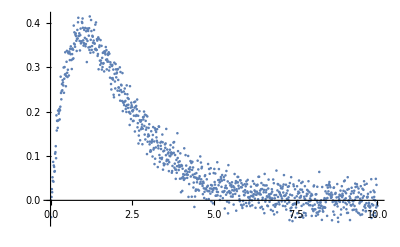
Show[-Graphics-,Plot[fit[t],{t,Min[times],Max[times]},PlotStyle→Red]]

```mathematica
model=a t^b+c;
fit=NonlinearModelFit[results,model,{a,b,c},t];
Show[ListPlot[results],Plot[fit[t],{t,Min[times],Max[times]},PlotStyle->Red]]
```

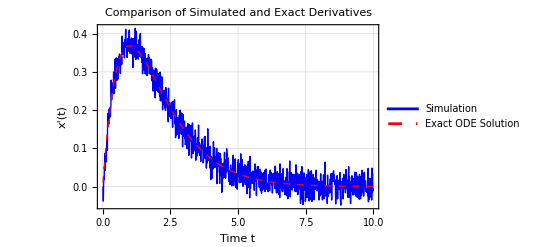

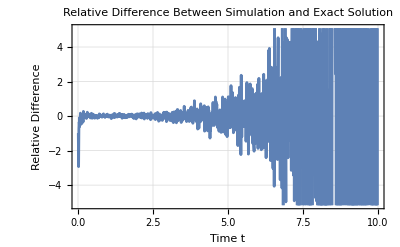

```mathematica
(*Parameters-must match your Python simulation*)gamma=0.999;
k=1.0;
tau=1.0;
F0=1.0;

(*Import the simulation data*)
simData=Import["average_derivative.dat","Table"];
simTimes=simData[[All,1]];
simDerivatives=simData[[All,2]];

(*Analytical solution of the ODE*)
odeSolution=DSolve[{gamma*x'[t]+k*x[t]==F0*(1-Exp[-t/tau]),x[0]==0 (*Initial condition*)},x[t],t];

(*Extract the solution and compute its derivative*)
xExact[t_]=x[t]/. First[odeSolution];
xPrimeExact[t_]=D[xExact[t],t];

(*Compute exact derivatives at simulation times*)
exactDerivatives=Table[xPrimeExact[t],{t,simTimes}];

(*Create comparison dataset*)
comparisonData=Transpose[{simTimes,simDerivatives,(*Simulation results*)exactDerivatives (*Exact solution*)}];

(*Plot comparison*)
ListPlot[{{simTimes,simDerivatives}//Transpose,{simTimes,exactDerivatives}//Transpose},Joined->True,PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red,Dashed}},Frame->True,FrameLabel->{"Time t","x'(t)"},PlotLegends->{"Simulation","Exact ODE Solution"},GridLines->Automatic,PlotLabel->"Comparison of Simulated and Exact Derivatives"]

(*Calculate and plot relative differences*)
relativeDiff=(simDerivatives-exactDerivatives)/exactDerivatives;
ListPlot[{simTimes,relativeDiff}//Transpose,Joined->True,Frame->True,FrameLabel->{"Time t","Relative Difference"},PlotLabel->"Relative Difference Between Simulation and Exact Solution",GridLines->Automatic]

(*Export comparison data*)
Export["derivative_comparison.dat",comparisonData,"Table"];
Export["relative_differences.dat",Transpose[{simTimes,relativeDiff}],"Table"];
```

Exact position solution: 1. ⅇ^(-1.001 t) (999.-1000. ⅇ^(0.001001 t)+1. ⅇ^(1.001 t))

Exact velocity solution: -1.001 ⅇ^(-1.001 t) (999.-1000. ⅇ^(0.001001 t)+1. ⅇ^(1.001 t))+1. ⅇ^(-1.001 t) (-1.001 ⅇ^(0.001001 t)+1.001 ⅇ^(1.001 t))

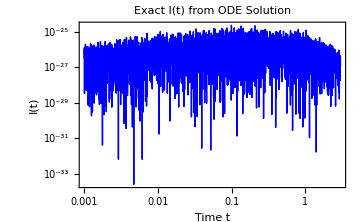

```mathematica
(*Parameters-must match your Python simulation*)gamma=0.999;
k=1.0;
tau=1.0;
F0=1.0;
T=1.0;
beta=1/T;  (*Inverse temperature*)

(*Exact solution of the ODE*)
odeSolution=DSolve[{gamma*x'[t]+k*x[t]==F0*(1-Exp[-t/tau]),x[0]==0 (*Initial condition*)},x[t],t];

(*Extract the solution and compute its derivative*)
xExact[t_]=x[t]/. First[odeSolution];
xPrimeExact[t_]=D[xExact[t],t];

(*Your I(t) function using exact derivatives*)
IofTExact[t_]:=(2 Sqrt[2] E^(-2 t (k/gamma+1/tau)) Pi Sqrt[k beta] ((-E^(((k t)/gamma))+E^(t/tau)) F0-E^(t (k/gamma+1/tau)) (gamma-k tau) xPrimeExact[t])^2)/((gamma-k tau)^2 Sqrt[k beta (1+Coth[(k t)/gamma])]);

(*Create time points for evaluation*)
tStart=0.001;  (*Avoid t=0 for numerical stability*)
tEnd=3.0;      (*Adjust based on your time range*)
timePoints=Subdivide[tStart,tEnd,300]; (*300 points like your simulation*)

(*Evaluate I(t) at these time points*)
IexactValues=Table[{t,IofTExact[t]},{t,timePoints}];

(*Plot the exact I(t)*)
exactPlot=LogLogPlot[IofTExact[t],{t,tStart,tEnd},PlotRange->All,Frame->True,FrameLabel->{"Time t","I(t)"},PlotLabel->"Exact I(t) from ODE Solution",GridLines->Automatic,PlotStyle->{Thick,Blue},ImageSize->Medium];

(*If you have simulation data to compare*)
(*simulationData=Import["simulation_results.dat","Table"];*)
(*comparisonPlot=ListLogLogPlot[simulationData,Joined->True,PlotStyle->Red];*)

(*Show both plots together*)
(*Show[exactPlot,comparisonPlot,PlotLegends->{"Exact","Simulation"}]*)

(*Export exact results*)
Export["exact_I_of_t.dat",IexactValues,"Table"];

(*Display the exact solution and its derivative*)
Print["Exact position solution: ",xExact[t]]
Print["Exact velocity solution: ",xPrimeExact[t]]
exactPlot
```

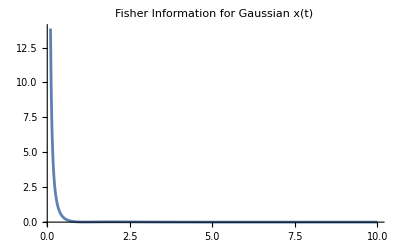

```mathematica
(*Assume mu[t] and sigma[t] are known*)mu[t_]:=F0/(k (gamma-k tau)) (E^(-k t/gamma)-E^(-t/tau)); (*Example*)
sigma[t_]:=Sqrt[T/k (1-E^(-2 k t/gamma))]; (*Example*)

(*Fisher information*)
FisherInfo[t_]:=(mu'[t]/sigma[t])^2+(1/2) (sigma'[t]/sigma[t])^2;

(*Plot*)
Plot[FisherInfo[t],{t,0.1,10},FrameLabel->{"Time t","Fisher Information ℐ(t)"},PlotLabel->"Fisher Information for Gaussian x(t)",PlotRange->All]
```